# Самостоятельная работа.

Выполнил студент ММФ  БГУ
КМ, 1 к, 3 гр . Шпак А . В .
 29 декабря 2021

## 1. Самостоятельная работа.

### Задание 1.

На плоскости заданы отрезок ab и точка p, лежащая на прямой L_ab несущей отрезок ab. Требуется определить положение точки p относительно отрезка ab. Варианты ответов: точка p, лежащая на прямой L_ab: 
0 - совпадает с точкой a;
1 - совпадает с точкой b;
2 - лежит на отрезке ab между точками a и b;
-1 - лежит вне отрезка ab на луче с началом в точке a;
3 - лежит вне отрезка ab на луче с началом в точке b.

```mathematica
(*Конструктор–оператор kmPoint, когда имя задано, в декартовой системе координат.*)
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord]
(*Так как у точки P есть соответствующее наименование, можно создать экземпляр объекта. Допустим, координаты точки следующие:*)
(*Точка P:*)
pointP=kmPoint["P",{1,5}]
```

kmPoint[km,P,{1,5}]

```mathematica
(*Свойство, если мне понадобится получить координаты:*)
kmPoint[km,id_String,coord_List,___]["coord"]:=coord;
pointP["coord"]
```

{1,5}

```mathematica
(*Свойство, которое мне понадобится, чтобы получить имя экземпляра объекта точка на плоскости:*)
kmPoint[km,id_String,__]["id"]:=id
pointP["id"]
```

P

```mathematica
(*Функция, которая мне понадобится, чтобы узнать, именован ли экземпляр объекта точка:*)
NamedQ[kmPoint[km,id_String,___]]^:=id!="";
```

```mathematica
(*Опишу предтавление нового объекта - отрезок прямой:*)
kmSegment[id_String,coordA_List,coordB_List]
(*Отрезок AB задам как новый объект с помощью конструктора:*)
kmSegment[pointP1_kmPoint,pointP2_kmPoint]:=kmSegment[If[And@@NamedQ/@{pointP1,pointP2},StringJoin[pointP1@"id",pointP2@"id"],"Отрезок"],pointP1["coord"],pointP2["coord"]];
```

kmSegment[id_String,coordA_List,coordB_List]

```mathematica
(*Создам точки A и B, начало и конец отрезка:*)
pointA=kmPoint["A",{5,8}]
pointB=kmPoint["B",{-3,1}]
(*Проверю, как сработает мой конструктор:*)
mySegment=kmSegment[pointA,pointB]
```

kmPoint[km,A,{5,8}]

kmPoint[km,B,{-3,1}]

kmSegment[AB,{5,8},{-3,1}]

```mathematica
(*Теперь мне понадобятся свойства для получения начала/конца отрезка:*)
kmSegment[id_String,pointP1Coord_List,pointP2Coord_List]["startPoint"]:=pointP1Coord
kmSegment[id_String,pointP1Coord_List,pointP2Coord_List]["endPoint"]:=pointP2Coord
(*Проверю свойства:*)
mySegment["startPoint"]
mySegment["endPoint"]
```

{5,8}

{-3,1}

```mathematica
(*Проверю, совпадают ли координаты точки P с точками A и B объекта отрезок. Сначала напишу функцию для проверки совпадения с A:*)
isSimilarWithA[pointP_kmPoint,segmentAB_kmSegment]:=If[pointP["coord"]==segmentAB["startPoint"],0,False]
isSimilarWithA[pointP]
isSimilarWithA[kmPoint["Random point 1",{5,8}]]
```

False

0

```mathematica
(*Функция проверки на совпадение с B:*)
isSimilarWithB[pointP_kmPoint,segmentAB_kmSegment]:=If[pointP["coord"]==segmentAB["endPoint"],1,False]
isSimilarWithB[pointP]
isSimilarWithB[kmPoint["Random point 2",{-3,1}]]
```

False

1

```mathematica
(*Точка принадлежит отрезку,если сумма расстояний от этой точки до конечных точек отрезка равна длине отрезка.*)
(*Функция,определяющая длину между двумя точками:*)
A={xa,ya}
B={xb,yb}
(A-B).(A-B)
Sqrt[(A-B).(A-B)]
getPointsDistance[pointP1Coord_List,pointP2Coord_List]:=Sqrt[(pointP1Coord-pointP2Coord).(pointP1Coord-pointP2Coord)]
```

{xa,ya}

{xb,yb}

(xa-xb)^2+(ya-yb)^2

√((xa-xb)^2+(ya-yb)^2)

```mathematica
(*Теперь напишу функцию, которая определит, принадлежит ли моя точка отрезку и каким именно образом:*)
isPointBelongsToSegment[pointP_kmPoint,segmentAB_kmSegment]:=If[getPointsDistance[segmentAB["startPoint"]
,segmentAB["endPoint"]]==(getPointsDistance[pointP["coord"]
,segmentAB["startPoint"]]+getPointsDistance[pointP["coord"]
,segmentAB["endPoint"]]),2,False]
isPointBelongsToSegment[pointP,mySegment]
```

False

```mathematica
(*Другой пример:*)
isPointBelongsToSegment[kmPoint["random point 3",{5,5}],kmSegment[kmPoint["C",{0,0}],kmPoint["D",{6,6}]]]
```

2

```mathematica
(*Опишу функцию, определяющей как именно будет лежать точка P, по отношению к точке A:*)
wherePointLays[pointP_kmPoint,segmentAB_kmSegment]:=If[getPointsDistance[segmentAB["startPoint"]
,segmentAB["endPoint"]]/2>getPointsDistance[pointP["coord"]
,segmentAB["startPoint"]],-1,3]
(*Проверю:*)
wherePointLays[pointP,mySegment]
```

-1

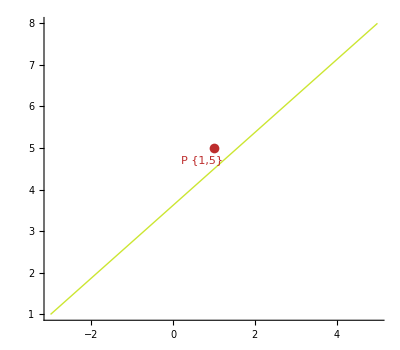

```mathematica
(*С рисунком будет проще:*)
Show[Graphics[{Hue[0.19,0.78,0.9],Line[{mySegment["startPoint"],mySegment["endPoint"]}],AbsolutePointSize[7],Hue[0,0.76,0.74],Point[pointP["coord"]],Text["P"Text[pointP["coord"]],pointP["coord"]-0.3]},PlotRange->All,Axes->True]]
```

### Задание 2.

Описание задания 2.

```mathematica
(*Input*)
```